```mathematica
yyyHankSingle[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t])/(8),{d,-7,7,2}]
```

```mathematica
yyyHankSingleRand[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t])/(20),{d,RandomVariate[UniformDistribution[{-7,7}],20]}];
```

```mathematica
DaForceSingleX[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],x];
DaForceSingleY[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],y];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

```mathematica
yyyHankSingle[x,y,t,k,w]
```

1/11 (BesselJ[0,k √(x^2+(-7+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-7+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-5+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-3+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-3+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(-1+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-1+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(1+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(1+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(3+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(3+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(5+y)^2)] Sin[t w])+1/11 (BesselJ[0,k √(x^2+(7+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(7+y)^2)] Sin[t w])

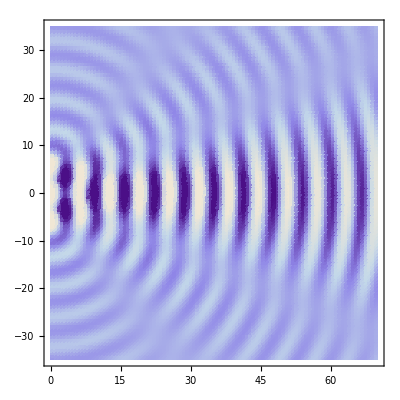

```mathematica
DensityPlot[yyyHankSingle[x,y,0,1,1],{x,0,70},{y,-35,35},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

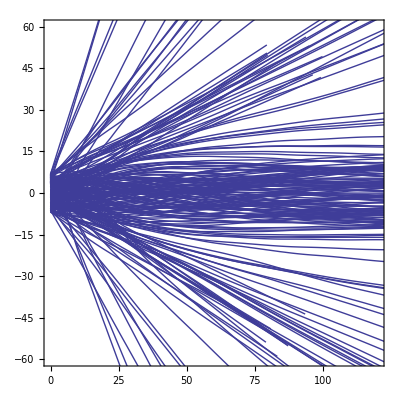

```mathematica
AAA =  1.0;
ddd = 7.0;
x000 = 0.0;
www=1;
v000 = 1.0;
kkk= 1;
disss = 0.01;
tmax = 200;
xmax = 120;
NMAX=200;
phase = -π;

Hollandtabl3DU=
Parallelize[
Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[SincSqWidth[2.0]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}]
];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
ddd =7.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.02;
tmax = 200;
swidth = 1;
phase = -1;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 50;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitPhase.dat"];

Do[

Hollandtabl3DU=
Parallelize[Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[SincSqWidth[2.0]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}]
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitPhase.dat

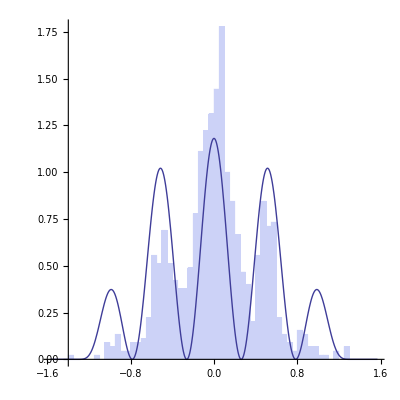

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitW7.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

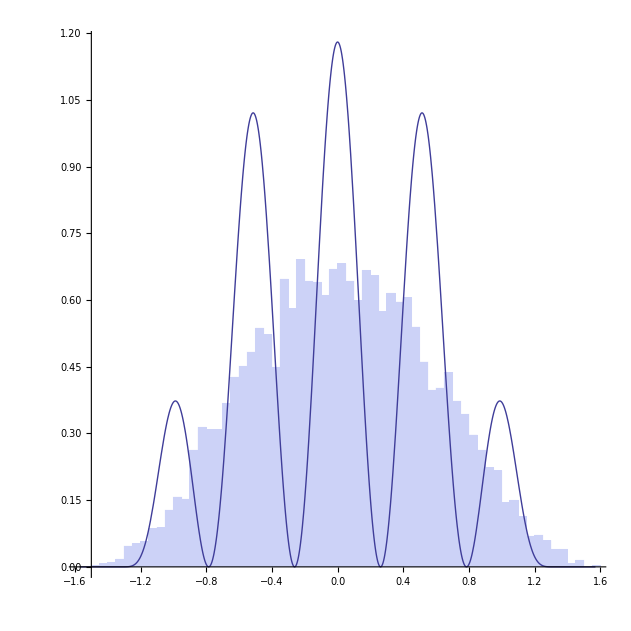

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M1.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

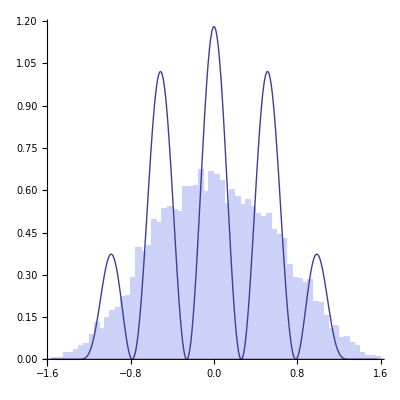

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M3.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

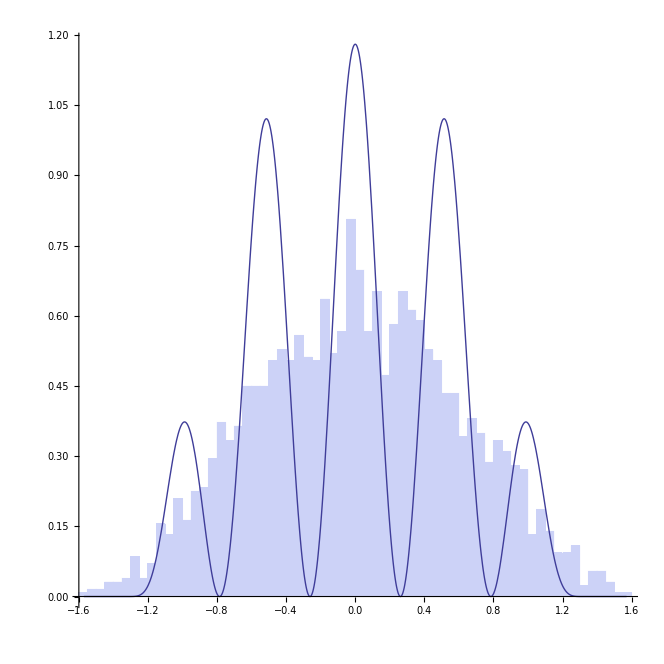

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M5.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

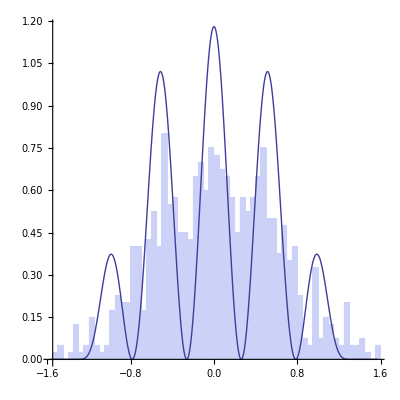

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M65.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

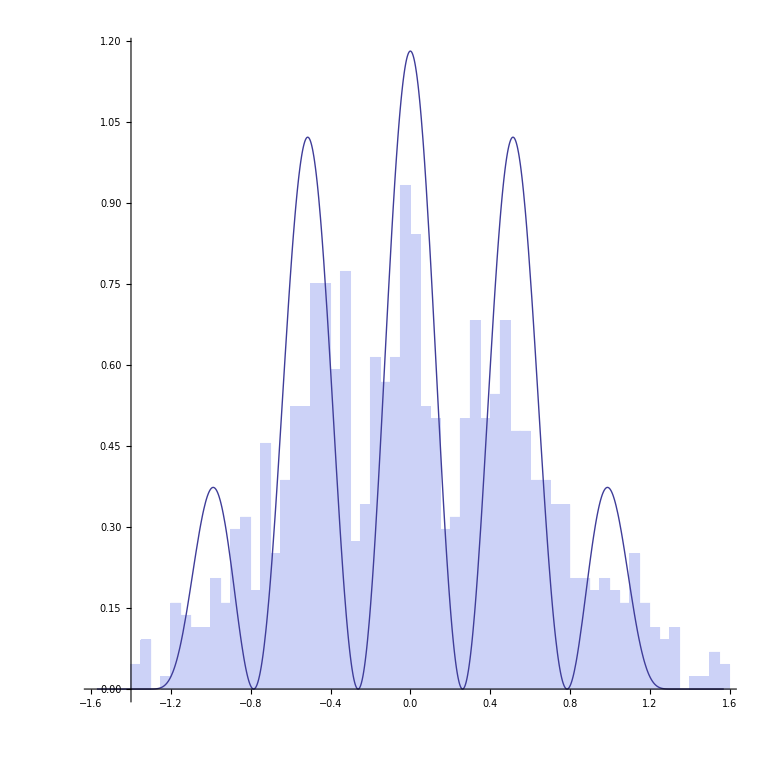

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M8.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

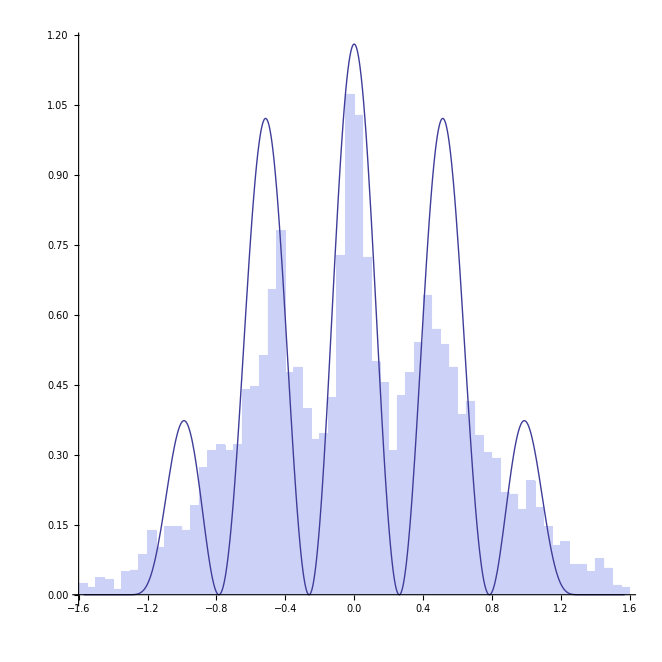

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M10.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

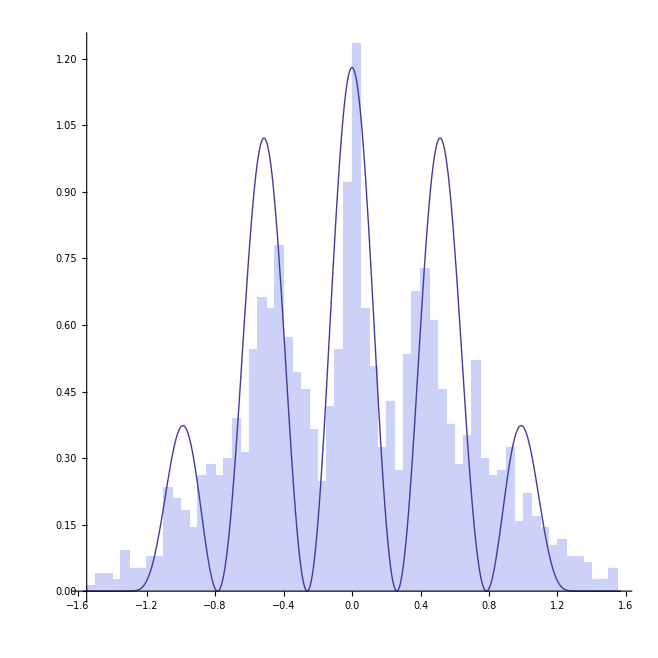

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M12.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

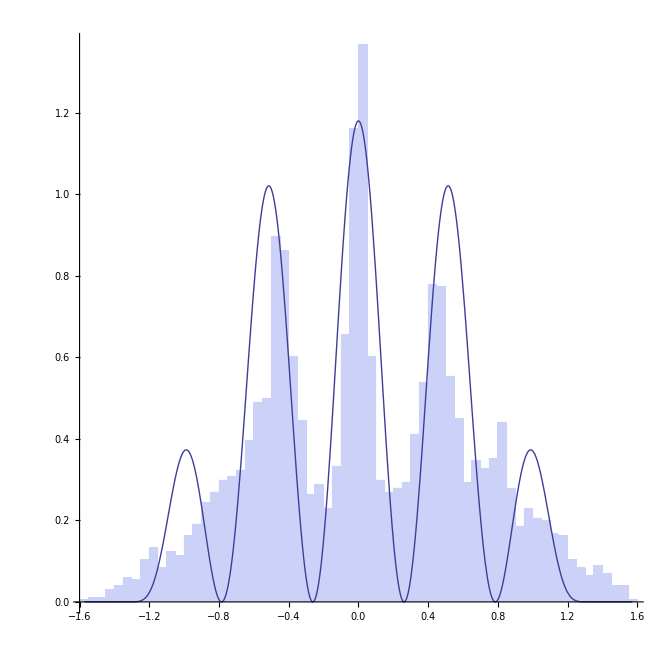

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M15.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

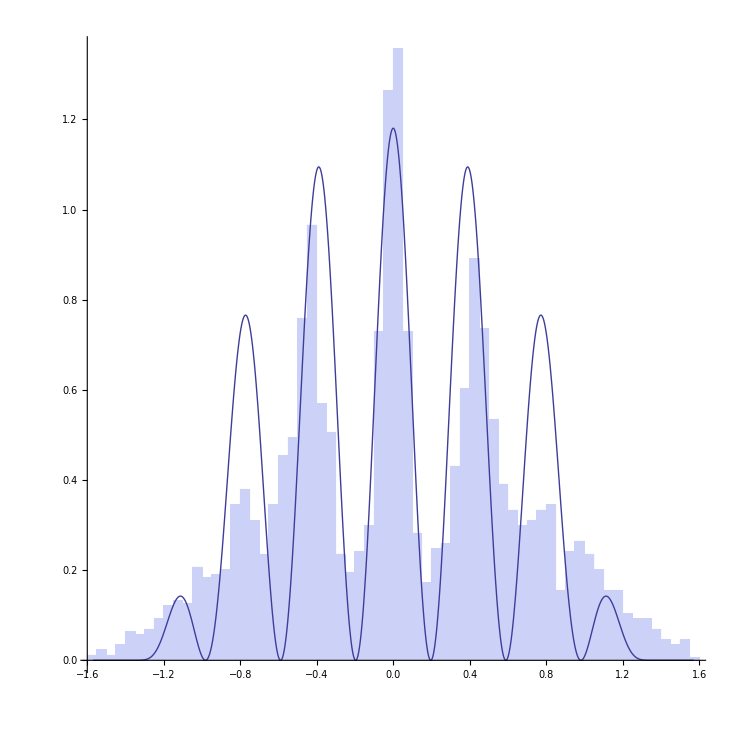

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M20.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[8x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

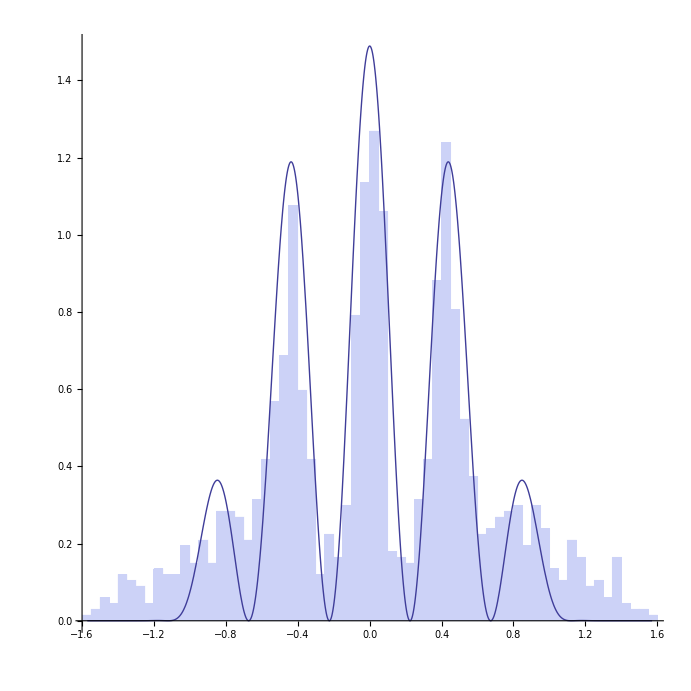

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M40.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.0^2))/(π Erfc[1/1.0])Cos[7x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

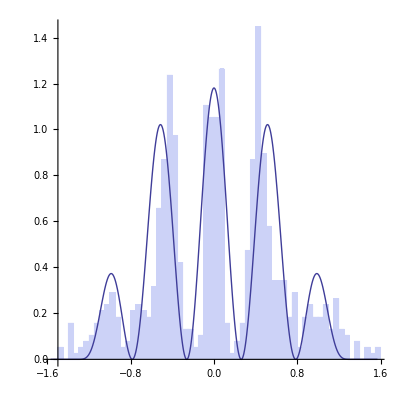

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M300.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[6x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

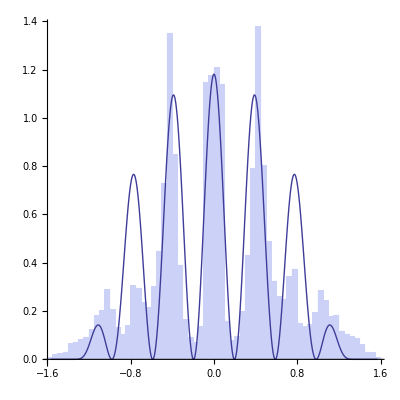

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/1.5^2))/(π Erfc[1/1.5])Cos[8x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```